## Section | Field Quantization

We introduce quantization of the electromagnetic field for a single mode using second quantization and show how it is implemented in Wolfram Mathematica via the Wolfram Quantum Framework. To make computations tractable we work in a truncated Fock space, then build operators and states, examine their algebra, and compute basic expectation values.

### Key Concepts

Quantization of electromagnetic field

Qudit representation of a field mode

Ladder operators

Vacuum fluctuations

### Quantization of a single mode field

The opening example that you usually find in most quantum textbook is the particle-in-a-box. In quantum optics, the “1-dimensional cavity along an axis such as z” is basically the simplest physical situation where all the core ideas show up clearly, without the messiness of real 3D geometry, complicated materials, or boundaries.

Let’s begin with a 1-dimensional cavity along the z axis with perfectly conducting walls at z=0 and z=L (two idea mirrors facing each other). We consider an empty cavity with no charges or currents. Because electromagnetic radiation is transverse, there are two independent polarization families; to keep the model minimal we choose a single polarization, say along x, so the electric field can be written as a fixed unit vector e_x  times a scalar amplitude that depends only on z and t. So one gets E(r,t) =e_x E_x (z,t)={E_x (z,t),0,0} . From Maxwell’s equations, Gauss for electric field, ∇.E=0, is automatically satisfied.

Confirm that ∇.E=0 is automatically satisfied for the ansatz E(r,t)  = e_x E_x (z,t):

```mathematica
ClearAll[Ex]
Div[{Ex[z,t],0,0},{x,y,z}]
```

0

The left-hand-side of Faraday equation, ∇×E=-∂_t B, implies that the magnetic field contains only y-component (B={0,B_y(z,t),0}):

```mathematica
Curl[{Ex[z,t],0,0},{x,y,z}]
```

{0,Ex^(1,0)[z,t],0}

Then the Gauss equation for magnetic field, ∇.B=0 is also automatically satisfied:

```mathematica
ClearAll[By]
Div[{0,By[z,t],0},{x,y,z}]
```

0

Therefore all four Maxwell equations reduce to two coupled first-order PDEs: ∂_z E_x(z,t)=-∂_t B_y(z,t) and -∂_z B_y(z,t)=μ_0 ϵ_0∂_t E_x(z,t). In other words, you started with four vector equations, but symmetry + transversality collapses them to two scalar dynamical relations, exactly one propagating degree of freedom (per polarization). From these equations, one can get standard wave equations ∂_(t,t) E_x=c^2∂_(z,z) E_x and ∂_(t,t) B_y=c^2∂_(z,z) B_y.

For ideal mirrors at z=0,L, the tangential electric field must vanish at the surface. Since 𝐸 is along x (tangential at those planes) the boundary conditions imply: E_x(0,t)=E_x(L,t)=0. The boundary conditions of electric field automatically imply ∂_z B_y(0,t)=∂_z B_y(L,t)=0.

Solve wave equation for the electric field:

```mathematica
DSolveValue[{D[Ex[z,t],{t,2}]==c^2 D[Ex[z,t],{z,2}],Ex[0,t]==0,Ex[L,t]==0},Ex[z,t],{z,t},Assumptions->c>0&&L>0]
```

Piecewise[{{√2 √(1/L) (Cos[(c π t K[1])/L] ∫_0^L √2 √(1/L) Ex[z,0] Sin[(π z K[1])/L]ⅆz+(L (∫_0^L (√2 Sin[(π z K[1])/L] Ex^(0,1)[z,0])/(√L)ⅆz) Sin[(c π t K[1])/L])/(c π K[1])) Sin[(π z K[1])/L]K[1]1∞, K[1]∈ℤ&&K[1]≥1}, {Indeterminate, True}}]

As one can see, the generic result as the form E_x(z,t)=∑_(n=1)^∞ q_n(t) sin((n π)/L z) where q_n(t)  is a time-dependent canonical coordinate of the mode n. The terms sin(k_n z) with the wave number k_n=n π/L are the spatial mode function of the cavity, i.e. a standing-wave eigenfunction (or normal mode) in the z-direction.

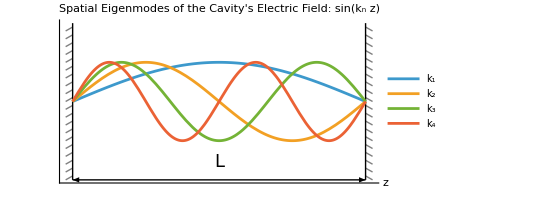

```mathematica
Show[{Graphics[{{Gray,Table[Line[{{0,1.9-.1(j-1)},{-.3,1.9-.1j}}],{j,1,40,2}],Table[Line[{{4π,1.9-.1(j-1)},{4π+.3,1.9-.1j}}],{j,1,40,2}]},{Line[{{0,-2},{0,2}}],Line[{{4Pi,-2},{4Pi,2}}],Arrowheads[{-.05,.05}],Arrow[{{0,-2},{4Pi,-2}}],Text[Style["L",18],{2Pi,-1.55}]}}],Plot[Evaluate@Table[Sin[k π x/(4Pi)],{k,4}],{x,0,4Pi},PlotLegends->Placed[{"k_1","k_2","k_3","k_4"},Below]]},Ticks->None,Axes->{True,False}, AxesLabel->{"z",""},ImageSize->400,PlotLabel->"Spatial Eigenmodes of the Cavity's Electric Field: sin(k_n z) "]
```

Solve wave equation for the magnetic field:

```mathematica
DSolveValue[{D[By[z,t],{t,2}]==c^2 D[By[z,t],{z,2}],Derivative[1,0][By][0,t]==0,Derivative[1,0][By][L,t]==0},By[z,t],{z,t},Assumptions->c>0&&L>0]
```

Piecewise[{{(∫_0^L By[z,0]/(√L)ⅆz+t ∫_0^L (By^(0,1)[z,0])/(√L)ⅆz)/(√L)+(√2 Cos[(π z K[1])/L] (Cos[(c π t K[1])/L] ∫_0^L (√2 By[z,0] Cos[(π z K[1])/L])/(√L)ⅆz+(L (∫_0^L (√2 Cos[(π z K[1])/L] By^(0,1)[z,0])/(√L)ⅆz) Sin[(c π t K[1])/L])/(c π K[1])))/(√L)K[1]1∞, K[1]∈ℤ&&K[1]≥1}, {Indeterminate, True}}]

As one can see, the generic result as the form B_y(z,t)=h_0+∑_(n=1)^∞ p_n(t) cos((n π)/L z) where p_n(t)=1/(c^2 k_n)(ⅆq_n(t))/ⅆt  is a time-dependent canonical momentum of the mode n. The terms cos(k_n z) are magnetic standing-wave mode function, and h_0 is the spatially uniform (static) magnetic field that represents a constant background magnetic field inside the cavity that does not vary with z and (in this idealized model) does not evolve in time.

The field energy, which plays the role of the Hamiltonian H, is: H=A/2∫_0^L (ϵ_0 E_x^2+1/μ_0^2 B_y^2)ⅆz with A the cross-section. Use orthogonality of sine/cosine modes, one finds: H=V/(2 μ_0)h_0^2+(ϵ_0 V)/4∑_(n=1)^∞ ((q_n(t))^2+c^2(p_n(t))^2) where V=A L. With rescaled mode variables Q_n=√((ϵ_0 V)/2)q_n/ω_n and P_n=√(V/(2 μ_0))p_n where ω_n=c k_n, one can rewrite the Hamiltonian as H=V/(2 μ_0)h_0^2+∑_(n=1)^∞ 1/2(P_n^2+ω_n^2 Q_n^2). This is the clean “harmonic oscillator decomposition” of the cavity field energy.

Using the Maxwell relations above, one can show that the rescaled variables satisfy: (ⅆQ_n(t))/ⅆt=P_n(t) and (ⅆP_n(t))/ⅆt=-ω_n^2Q_n(t). In other words, these canonical variables evolve exactly like oscillator coordinate and momentum. Without losing generality, one can drop h_0 from the Hamiltonian. Also, instead of all modes in the Hamiltonian (i.e. summation over n), one can consider only a single mode case. In many quantum optics situations, only one cavity resonance matters and we shall consider that one, only. Therefore, the Hamiltonian becomes H=1/2(P^2+ω^2 Q^2).

In a similar manner, the electric and magnetic fields would be given by E_x(z,t)=√(2/(ϵ_0 V))ω Q(t) sin(k z) and B_y(z,t)=√((2 μ_0)/V) P(t) cos(k z). Now let’s clarify an important fact. The variables Q and P are not arbitrary—they are the canonical coordinate and momentum of cavity mode. Q(t) is the “electric-like quadrature”. P(t) is the “magnetic-like quadrature”. In quantum theory, they become noncommuting quadrature operators (like position and momentum), and their phase-space structure leads directly to uncertainty, vacuum noise, coherent states, squeezing, etc. Let’s explore some more details for Q and P.

Recall the coupled first-order system for canonical variables is (ⅆQ(t))/ⅆt=P(t) and (ⅆP(t))/ⅆt=-ω^2Q(t). Thus one finds: (ⅆ^2 Q(t))/(ⅆ t^2)=-ω^2Q(t). That is the standard harmonic oscillator equation.

Solve harmonic oscillator equation for Q(t):

```mathematica
DSolveValue[{D[Q[t],{t,2}]==-ω^2 Q[t],Q[0]==Q0,Derivative[1][Q][0]==P0},Q[t],t]//FullSimplify
```

Q0 Cos[t ω]+(P0 Sin[t ω])/ω

Given the solution, find P(t) using (ⅆQ(t))/ⅆt=P(t):

```mathematica
D[%,t]
```

P0 Cos[t ω]-Q0 ω Sin[t ω]

It can be shown that the transformation from the pair (ω Q_0
_P_0) into (ω Q(t)
_(P(t))) is described by a rotation in phase space at angular frequency ω:

```mathematica
RotationMatrix[-ω t].{ω Subscript[Q, 0],Subscript[P, 0]}
```

{Sin[t ω] P_0+ω Cos[t ω] Q_0,Cos[t ω] P_0-ω Sin[t ω] Q_0}

Therefore, the time-dependent electric and magnetic fields become E_x(z,t)=√(2/(ϵ_0 V))sin(k z)(ω Q_0 cos(ω t)+P_0 sin(ω t)) and B_y(z,t)=√((2 μ_0)/V)cos(k z)(-ω Q_0 sin(ω t)+P_0 cos(ω t)).

Quantization promotes the canonical variables P and Q to operators P̂ and Q̂ that satisfy the canonical commutation relation: [Q̂,P̂]=ⅈℏ. With these operators, the Hamiltonian becomes: Ĥ=1/2((P̂)^2+ω^2(Q̂)^2).

It is standard to introduce the non-Hermitian (non-observable) ladder operators â and (â)^†, which simplify the algebra and encode how the field exchanges quanta: â=√(ω/(2ℏ))(Q̂+ⅈ/(√(2ℏ ω))P̂) and (â)^†=√(ω/(2ℏ))(Q̂-ⅈ/(√(2ℏ ω))P̂).

The ladder operators â and (â)^† satisfy the commutation relation [â,(â)^†]=1. Consequently, the Hamiltonian can be written as Ĥ=ℏ ω ((â)^†â+1/2). Additionally, the operators for electric and magnetic fields become (Ê)_x(z,t)=√((ℏ ω)/(ϵ_0 V))sin(k z)(â ⅇ^(-ⅈ ω t)+(â)^† ⅇ^(ⅈ ω t)) and (B̂)_y(z,t)=-ⅈ √((μ_0 ℏ ω)/V)cos(k z)(â ⅇ^(-ⅈ ω t)-(â)^† ⅇ^(ⅈ ω t)).

The operator (â)^†â is called the number operator and is also Hermitian with eigenstates n where (â)^†â n=nn. The commutation relations [(â)^†â,â]=-â and [(â)^†â,(â)^†]=(â)^† can be obtained from [â,(â)^†]=1 and useful identity such as [A B,C]= A [B,C]+ [A,C] B. These commutators tell you how eigenvalues shift: (â)^† raises n while â lowers n; and all together n>=0 and must be integer. We will explore these properties computationally.

For eigenstate n, the Hamiltonian eigenvalue equation becomes Ĥ n=E_n n with E_n=ℏω(n+1/2). The eigenstate 0 is usually called the vacuum state and n the n-photon Fock state. Because there’s no upper limit to how many photons you could, in principle, have, you need infinitely many basis states, i.e., n goes to infinity. That’s why this Hilbert space is infinite-dimensional. Fock space is simply the name for a Hilbert space organized by n. You can think of it as being built from “sectors” with fixed numbers of quanta: there’s a vacuum sector (no quanta), a one-quantum sector, a two-quantum sector, etc. For a single mode (which is the case we are focused now), each sector is one-dimensional and the whole space looks like an infinite ladder of number states. For many modes, Fock space contains all combinations of occupation numbers across modes.

-Graphics-

The creation and annihilation operators raise or lower a state with an energy increase or decrease of ℏω. They are bosonic ladder operators that create or annihilate a photon. We shall explore properties of these operators in the following section.

### Basic properties of creation and annihilation operators

In numerical work we approximate the infinite-dimensional Fock space with a finite photon-number cutoff, so calculations live in a finite-dimensional subspace. The cutoff sets the maximum occupation per mode (or globally across modes) and trades accuracy for computational cost. With this choice, basis states and operators become finite matrices on the truncated tensor-product space.

Set the photon-number cutoff to 12:

```mathematica
SetFockSpaceSize[12];
```

This truncation is the main approximation in what follows: we restrict the infinite-dimensional Hilbert space to a finite-dimensional subspace by limiting the maximum excitation number.

Use $FockSize to see the current cutoff.

```mathematica
$FockSize
```

12

Display the truncated Fock-space basis:

```mathematica
QuantumBasis[$FockSize]//TraditionalForm
```

<|0→{1,0,0,0,0,0,0,0,0,0,0,0},1→{0,1,0,0,0,0,0,0,0,0,0,0},2→{0,0,1,0,0,0,0,0,0,0,0,0},3→{0,0,0,1,0,0,0,0,0,0,0,0},4→{0,0,0,0,1,0,0,0,0,0,0,0},5→{0,0,0,0,0,1,0,0,0,0,0,0},6→{0,0,0,0,0,0,1,0,0,0,0,0},7→{0,0,0,0,0,0,0,1,0,0,0,0},8→{0,0,0,0,0,0,0,0,1,0,0,0},9→{0,0,0,0,0,0,0,0,0,1,0,0},10→{0,0,0,0,0,0,0,0,0,0,1,0},11→{0,0,0,0,0,0,0,0,0,0,0,1}|>

The basis is indexed in the usual way, from 0 to $FockSize-1.

Define a as the annihilation operator:

```mathematica
a := AnnihilationOperator[];
```

The annihilation operator can take optional arguments (for example, to label modes); we will discuss these later.

Evaluate a:

```mathematica
a
```

QuantumOperator[…]

The summary box represents a quantum object (here a QuantumOperator) in the Wolfram Quantum Framework. Use Command+Shift+T or Control+Shift+T, or wrap with TraditionalForm, to view the symbolic form.

Show the Dirac notation for a:

```mathematica
a//TraditionalForm
```

01+√2 12+√3 23+234+√5 45+√6 56+√7 67+2 √278+389+√10 910+√11 1011

Changing the cutoff changes the operator dimension. Prefer using SetFockSpaceSize rather than directly modifying the global variable.

```mathematica
Block[{$FockSize = 16},a]
```

QuantumOperator[…]

The annihilation operator is fundamental because most Hamiltonians in Fock space can be written in terms of annihilation and creation operators. The creation operator can be obtained from the annihilation operator using SuperDagger (or the "Dagger" property), following standard quantum-mechanics notation.

Define the creation operator:

```mathematica
SuperDagger[a]
```

QuantumOperator[…]

Matrix elements of creation operator :

```mathematica
Rasterize[SuperDagger[a]["Table"],RasterSize->2000]
```

-Graphics-

The creation and annihilation operators are non-Hermitian and obey the commutator . In the truncated space the commutator deviates at the edge (note the last diagonal element), which is one manifestation of truncation error:

Compute the commutator of the annihilation and creation operators:

```mathematica
Commutator[a,SuperDagger[a]]//TraditionalForm
```

00+11+22+33+44+55+66+77+88+99+1010+1111+1212+1313+1414+1515+1616+1717+1818+1919+2020+2121+2222+2323+2424+2525+2626+2727+2828-292929

Pay attention to the last term, which is an artifact of truncation.

Pick an arbitrary n within the cutoff to verify how the ladder operators act on Fock states.

```mathematica
n = RandomInteger[{1,$FockSize -2}];
```

Verify the relation :

```mathematica
a @ FockState[n] == √n FockState[n-1]
```

True

Verify the relation :

```mathematica
SuperDagger[a] @ FockState[n] == √(n+1)FockState[n+1]
```

True

Repeated application of the annihilation operator eventually takes any Fock state to the vacuum, and one more application yields the zero vector.

```mathematica
NestList[a,FockState[$FockSize -1],$FockSize]//TraditionalForm
```

{11,√11 10,√110 9,3 √1108,12 √557,12 √3856,12 √23105,60 √4624,120 √4623,360 √1542,720 √771,720 √770,0}

Conversely, the nth Fock state can be constructed from the vacuum as follows:

Verify the relation above:

```mathematica
((SuperDagger[a])^n/(√(n!)))@FockState[0] == FockState[n]
```

True

Define the photon-number operator (an observable):

```mathematica
numberOp:=SuperDagger[a]@ a
```

Verify :

```mathematica
numberOp @ FockState[n] == n FockState[n]
```

True

Create a random pure state in the truncated Fock space:

```mathematica
st=QuantumState["RandomPure",$FockSize]
```

QuantumState[…]

Compute the mean photon number in three equivalent ways:

Bra-ket evaluation ψ a^†aψ:

```mathematica
st["Dagger"][numberOp[st]]["Scalar"]//Chop
```

4.12517

Using the "Mean" property of a QuantumMeasurement:

```mathematica
(QuantumMeasurementOperator[numberOp]@st)["Mean"]
```

4.12517

Mean value from probabilities and eigenvalues:

```mathematica
KeyValueMap[#1[[1]] #2 &, st["Probability"]]//Total
```

4.12517

### Quantum fluctuations for a single mode field

Define the electric-field operator :

```mathematica
Ex := ⅈ √((h ω)/(2 Subscript[ϵ, 0] V))(a Exp[ⅈ(Dot[k,r]-ω t)]-SuperDagger[a] Exp[-ⅈ(Dot[k,r]-ω t)]);
```

The energy eigenstate |n⟩ has a definite energy but no definite electric field. Using the ladder-operator action, it is straightforward to show that any Fock state has zero mean field:

Verify   :

```mathematica
(SuperDagger[#]@ Ex@#)& /@ Array[FockState,$FockSize-1,0]//TraditionalForm
```

{0,0,0,0,0,0,0,0,0,0,0}

However, the mean of the squared electric field is not zero; therefore the field has nonzero variance for all Fock states:

```mathematica
(#["Dagger"]@(Ex@Ex) @ #)["Scalar"]& /@ Table[FockState[n],{n,0,$FockSize-2}]//FullSimplify
```

{(h ω)/(2 V ϵ_0),(3 h ω)/(2 V ϵ_0),(5 h ω)/(2 V ϵ_0),(7 h ω)/(2 V ϵ_0),(9 h ω)/(2 V ϵ_0),(11 h ω)/(2 V ϵ_0),(13 h ω)/(2 V ϵ_0),(15 h ω)/(2 V ϵ_0),(17 h ω)/(2 V ϵ_0),(19 h ω)/(2 V ϵ_0),(21 h ω)/(2 V ϵ_0)}

You can also compute the variance directly with OperatorVariance for Fock states:

```mathematica
Table[OperatorVariance[FockState[i],Ex],{i,0,$FockSize-2}]
```

{(h ω)/(2 V ϵ_0),(3 h ω)/(2 V ϵ_0),(5 h ω)/(2 V ϵ_0),(7 h ω)/(2 V ϵ_0),(9 h ω)/(2 V ϵ_0),(11 h ω)/(2 V ϵ_0),(13 h ω)/(2 V ϵ_0),(15 h ω)/(2 V ϵ_0),(17 h ω)/(2 V ϵ_0),(19 h ω)/(2 V ϵ_0),(21 h ω)/(2 V ϵ_0)}

For an operator, the variance is defined as , and the standard deviation (uncertainty) is its square root. For a number state we obtain:

Even when n = 0 the mean field is zero but the uncertainty is not; this is vacuum fluctuations. This follows from the uncertainty principle because n̂ and OverHat[E_x] do not commute.

### Quadrature operators of a single mode field

Define the quadrature operators:

They are supported calling the following function:

```mathematica
{X1,X2}=QuadratureOperators[];
```

Quadratures describe the field in optical phase space, and their commutator mirrors the position-momentum relation .

The last term deviates because of truncation:

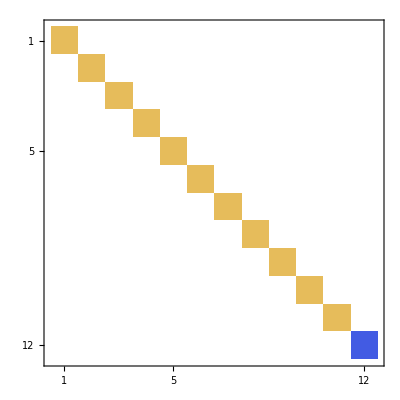

```mathematica
MatrixPlot[(Commutator[X1,X2]/(ⅈ/2))["Matrix"]]
```

You can derive the commutator exactly using the non-commutative algebra tools (version 14.3 and later):

Define the fundamental non-commuting variables and the quadratures :

```mathematica
vars = {a,SuperDagger[a]};
{X1symb, X2symb} = {1/2(a+SuperDagger[a]), 1/(2ⅈ)(a-SuperDagger[a])};
```

Define the commutation relation:

```mathematica
rel = {Commutator[a, SuperDagger[a]]-1};
```

Reduce the commutator of the quadratures:

```mathematica
NonCommutativePolynomialReduce[Commutator[X1symb,X2symb],rel,vars][[-1]]
```

ⅈ/2

For a Fock state we find . The ground state |0⟩ attains the minimum value 1/4:

```mathematica
Table[{
OperatorVariance[FockState[n],X1],
OperatorVariance[ FockState[n],X2]} ,
{n,0,$FockSize-2}]
```

{{1/4,1/4},{3/4,3/4},{5/4,5/4},{7/4,7/4},{9/4,9/4},{11/4,11/4},{13/4,13/4},{15/4,15/4},{17/4,17/4},{19/4,19/4},{21/4,21/4}}

### Thermal fields

Consider a single-mode field in thermal equilibrium in a cavity at temperature T. Statistical mechanics gives the photon-number distribution P_n that the n-th level is excited is:

where k_B is the Boltzmann constant

Using the Hamiltonian , the thermal (mixed) state is described by a density operator built from this distribution:

The denominator is the partition function:

Energy eigenvalues:

```mathematica
Clear[n]
En = h ω (n + 1/2);
```

The partition function Z is:

```mathematica
Z =Sum[Exp[-En/(kb T)],{n,0,∞}]
```

ⅇ^((h ω)/(2 kb T))/(ⅇ^((h ω)/(kb T))-1)

The probability of finding n photons is:

The average photon number is .

```mathematica
Sum[n Exp[-En/(kb T)],{n,0,∞}]/Z
```

1/(ⅇ^((h ω)/(kb T))-1)

ρ_Th can be written in terms of n^— (mean number of photons)as:

Construct a thermal state in the Quantum Framework with n^— = 0.8:

```mathematica
ρthermal = ThermalState[0.8];
```

Visualize the density matrix:

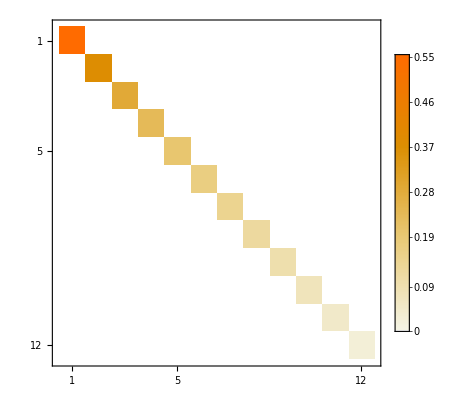

```mathematica
MatrixPlot[ρthermal["DensityMatrix"],PlotLegends->Automatic]
```

Compute the mean photon number:

```mathematica
(QuantumMeasurementOperator[numberOp]@ρthermal)["Mean"]
```

0.799287

Increase the Fock-space size:

```mathematica
SetFockSpaceSize[50];
```

Plot the photon-number distribution as the mean occupation n^— varies:

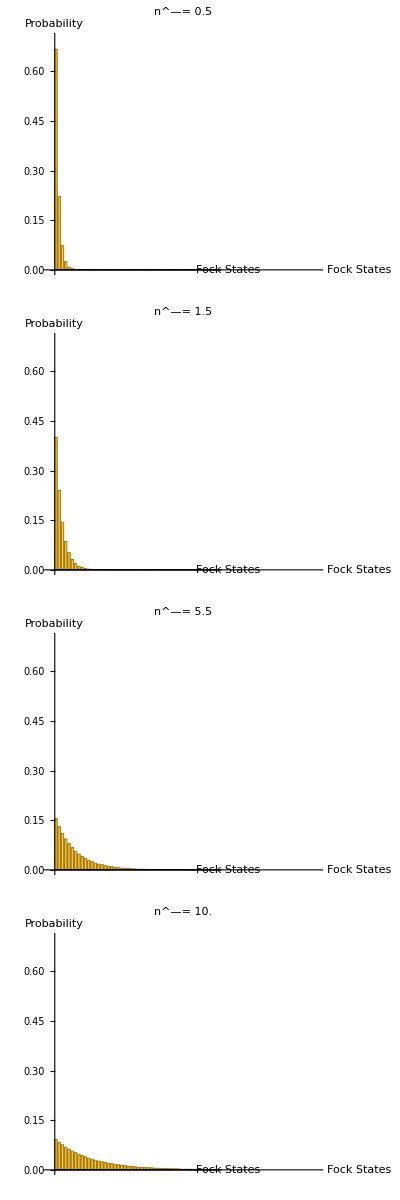

```mathematica
Table[ThermalState[x]["ProbabilitiesPlot",],{x,{0.5,1.5,5.5,10.}}]//Column
```

### The quantum phase

There have been many attempts to define a quantum phase. Dirac proposed a polar decomposition and assumed a Hermitian phase operator. However, it can be shown that exp(ⅈ ϕ̂) cannot be unitary; hence ϕ̂ cannot be Hermitian. Barnett and Pegg proposed unitary operators of the form e^(ⅈ ϕ̂), but that construction introduces unphysical negative-number states and does not add new physical predictions. Additional difficulties arise because ϕ̂ must be an angle operator, which leads to problematic relations when angular momentum is considered.

We follow the formalism introduced by Susskind and Glogower. The Susskind-Glogower operator Susskind is defined by:

Reset to the default Fock-space size (16) used when the paclet loads:

```mathematica
SetFockSpaceSize[]
```

16

Calculate Ê from the definition:

```mathematica
((SuperDagger[a]@a+1)^(-1/2))@a//TraditionalForm
```

01+12+23+34+45+56+67+78+89+910+1011+1112+1213+1314+1415

Equivalent expressions for these operators are:

and  (in each case we obtain N-1 terms, where N is the truncated space dimension).

Define the operator:

```mathematica
Ephase := QuantumOperator[DiagonalMatrix[Table[1,$FockSize-1],1],$FockSize]
```

```mathematica
Ephase//TraditionalForm
```

01+12+23+34+45+56+67+78+89+910+1011+1112+1213+1314+1415

Calculate  :

```mathematica
Ephase@SuperDagger[Ephase]//TraditionalForm
```

00+11+22+33+44+55+66+77+88+99+1010+1111+1212+1313+1414

Calculate :

```mathematica
SuperDagger[Ephase]@Ephase//TraditionalForm
```

11+22+33+44+55+66+77+88+99+1010+1111+1212+1313+1414+1515

Clearly the operator is not Hermitian:

```mathematica
Ephase["HermitianQ"]
```

False

Ê and (Ê)^† are not observables, but the combinations  and      act as analogs of cos(ϕ) and sin(ϕ):

```mathematica
Cphase = 1/2(Ephase+SuperDagger[Ephase]);
Sphase = 1/(2ⅈ)(Ephase -SuperDagger[Ephase]);
```

These operators are Hermitian and obey the commutator  (in the truncated basis the last term is affected by truncation).

```mathematica
Commutator[Cphase,Sphase]//TraditionalForm
```

ⅈ/2 00-ⅈ/21515

The trigonometric identity cos^2 + sin^2 = 1 has an analogous operator form, except for a vacuum term (Ĉ)^2+(Ŝ)^2 =1-1/2|0⟩⟨0| (and a small truncation error in the last term):

```mathematica
(Cphase@Cphase + Sphase@Sphase)//TraditionalForm
```

1/2 00+11+22+33+44+55+66+77+88+99+1010+1111+1212+1313+1414+1/2 1515

The following commutators can be shown and are useful for uncertainty relations:

```mathematica
Commutator[Cphase,numberOp] == ⅈ Sphase
```

True

```mathematica
Commutator[Sphase,numberOp]== -ⅈ Cphase
```

True

For number states  we have  and , hence

Then for n>=1, ΔC=ΔS=1/(√2) and 1/2 if n=0:

```mathematica
Partition[√OperatorVariance[FockState[#],#2]&@@@Tuples[{Range[0,$FockSize-2],{Cphase,Sphase}}],2]
```

{{1/2,1/2},{1/(√2),1/(√2)},{1/(√2),1/(√2)},{1/(√2),1/(√2)},{1/(√2),1/(√2)},{1/(√2),1/(√2)},{1/(√2),1/(√2)},{1/(√2),1/(√2)},{1/(√2),1/(√2)},{1/(√2),1/(√2)},{1/(√2),1/(√2)},{1/(√2),1/(√2)},{1/(√2),1/(√2)},{1/(√2),1/(√2)},{1/(√2),1/(√2)}}

The eigenstates |ϕ⟩ of the exponential operator satisfy the eigenvalue equation  and are defined by .

```mathematica
phistate := QuantumState[Table[ⅇ^(ⅈ n ϕ),{n,0,$FockSize-1}],$FockSize,"Parameters"->ϕ]
phistate//TraditionalForm
```

0+ⅇ^(ⅈ ϕ)1+ⅇ^(2 ⅈ ϕ)2+ⅇ^(3 ⅈ ϕ)3+ⅇ^(4 ⅈ ϕ)4+ⅇ^(5 ⅈ ϕ)5+ⅇ^(6 ⅈ ϕ)6+ⅇ^(7 ⅈ ϕ)7+ⅇ^(8 ⅈ ϕ)8+ⅇ^(9 ⅈ ϕ)9+ⅇ^(10 ⅈ ϕ)10+ⅇ^(11 ⅈ ϕ)11+ⅇ^(12 ⅈ ϕ)12+ⅇ^(13 ⅈ ϕ)13+ⅇ^(14 ⅈ ϕ)14+ⅇ^(15 ⅈ ϕ)15

As expected from how Ê acts on Fock states,, the last term fails the eigenstate equation in the truncated space:

```mathematica
( Ephase@phistate-ⅇ^(ⅈ ϕ) phistate)["AmplitudesList"]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅇ^(16 ⅈ ϕ)}

The phase eigenstates resolve the identity:

Compute the phase-eigenstate projectors:

```mathematica
phiProj =FullSimplify[QuantumOperator[(phistate @SuperDagger[phistate]),$FockSize],Element[ϕ,Reals]];
```

Verify that integrating the matrix elements yields the identity operator:

```mathematica
QuantumOperator[1/(2π)Integrate[phiProj["Matrix"],{ϕ,0,2π}],$FockSize] == QuantumOperator["I"[$FockSize]]
```

True

For a state |ψ⟩, the phase distribution 𝒫(ϕ) is computed as:

This distribution can be used to compute averages of functions of ϕ.

For any number state |n⟩ the phase distribution is uniform, 𝒫(ϕ) = 1/(2π). It has mean π and fluctuations Δϕ = π/√3. This holds for all number states, including the vacuum.

Phase distribution for Fock States:

```mathematica
Simplify[1/(2π)Abs[(phistate["Dagger"]@#)["Scalar"]]^2& /@ Array[FockState,$FockSize-1,0],ϕ∈Reals]
```

{1/(2 π),1/(2 π),1/(2 π),1/(2 π),1/(2 π),1/(2 π),1/(2 π),1/(2 π),1/(2 π),1/(2 π),1/(2 π),1/(2 π),1/(2 π),1/(2 π),1/(2 π)}

Mean and standard deviation:

```mathematica
Through[{Mean,StandardDeviation}[UniformDistribution[{0,2 π}]]]
```

{π,π/(√3)}

Other approaches to the quantum phase exist, but this one is supported by quantum estimation theory and yields a probability operator associated with maximum-likelihood phase estimation. Since there is no unique phase operator, Susskind-Glogower operators provide a reasonable qualitative description of a quantum phase variable.

##### Initialization

Install the Quantum Framework paclet (if needed):

```mathematica
PacletInstall["https://www.wolfr.am/DevWQCF",ForceVersionInstall->True]
```

PacletObject[…]

Load the Quantum Framework package:

```mathematica
Needs["Wolfram`QuantumFramework`"]
```

Load the second-quantization functionality:

```mathematica
Needs["Wolfram`QuantumFramework`SecondQuantization`"]
```

Vocabulary

AnnihilationOperator |   | defines the bosonic annihilation operator in
a finite dimensional space
FockState[n] |   | represents the states of the truncated Fock space basis
for a single mode
QuadratureOperators |   | returns the position and momentum quadrature
operators in a finite dimensional space
OperatorVariance |   | calculates the variance of an operator for a 
particular state
ThermalState |   | defines a quantum thermal state following the
canonical ensemble formalism

Exercises

Considering a thermal state with x mean number of photons. What happens to the mean number of photons after applying the annihilation operator? Do a plot

Solution

Surprisingly it doubles, note the state becomes not normalized after the annihilation operator application:

Plot[{x,Evaluate[(QuantumMeasurementOperator[numberOp]@(a@ThermalState[x]))["Mean"]]},{x,0,1},AxesLabel->{"x","⟨n⟩"}]

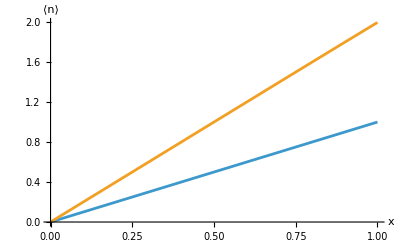

We can check that if we normalize the state, mean number of photons doubles so the previous plot is valid:

ψ =a[ThermalState[0.6]]["Normalize"];

Tr[numberOp["Matrix"].ψ["DensityMatrix"]]

1.19994

Define a maximally mixed state in the truncated Fock basis

Solution

One possible solution:

QuantumState["UniformMixture",$FockSize]

1/16 00+1/16 11+1/16 22+1/16 33+1/16 44+1/16 55+1/16 66+1/16 77+1/16 88+1/16 99+1/16 1010+1/16 1111+1/16 1212+1/16 1313+1/16 1414+1/16 1515

Alternative solution:

QuantumOperator["I"[$FockSize]]/$FockSize

1/16 00+1/16 11+1/16 22+1/16 33+1/16 44+1/16 55+1/16 66+1/16 77+1/16 88+1/16 99+1/16 1010+1/16 1111+1/16 1212+1/16 1313+1/16 1414+1/16 1515

Calculate the commutator of the number operator with the annihilation operator (suggested to use non commutative algebra)

Solution

NonCommutativePolynomialReduce[Commutator[a^†**a,a],{Commutator[a,a^†]-1},{a,a^†}][[-1]]

-a

Compute the phase distribution for the state 1/(√2)(|0⟩ + |1⟩ ). Is it still uniform? Prove it is a proper probability distribution

Solution

Calculate the phase distribution:

1/(2π)Abs[(phistate["Dagger"]@QuantumState["+",$FockSize])["Scalar"]]^2

(Abs[ⅇ^(-ⅈ Conjugate[ϕ])/(√2)+1/(√2)]^2)/(2 π)

Simplify the expression:

FullSimplify@ComplexExpand[%]

(cos(ϕ)+1)/(2 π)

Integrate over all the phases:

Integrate[%,{ϕ,-π,π}]

1

Show numerically 𝒫(ϕ) = 1/(2π) for a thermal state

A thermal state is not a pure state, so to calculate the phase distribution we use  𝒫(ϕ) = ⟨ ϕ | ρ_thermal | ϕ ⟩, let’s pick n^— = 0.5 . Use “Operator” property to treat the quantum state as an operator:

ϕthermal =1/(2π)Simplify[(phistate^†@ThermalState[0.5]["Operator"]@phistate)["Scalar"],ϕ ∈ Reals];

Numerically equivalent to the uniform distribution:

Abs[ϕthermal-1/(2π)]

3.69726×10^-9

Consider the superposition state |ψ⟩ = α |0⟩ + β |1⟩ , where α and β are complex and satisfy |α|^2+|β|^2. Calculate the variances of the operators X_1 and X_2. Are there any values of the parameters α and β for which either of the quadratures becomes less than for a vacuum state? If so, check if the uncertainty principle is violated

Solution

Defining the superposition:

ψ = α FockState[0]+β FockState[1]

α0+β1

Calculating the variances of the quadrature operators, without loss of generality we take α real, the replacement is to do a plot as function of |α|^2:

variances =FullSimplify[(OperatorVariance[ψ,#]&/@QuadratureOperators[])//.{β->√(1-Abs[α]^2)ⅇ^(ⅈ ϕ)},Element[{ϕ},Reals]&& 0<α<=1]/.α->√x;

Plots of the variances considering ϕ=0, the extreme cases are just the quadrature variances of |0⟩ and |1⟩:

Plot[Evaluate[Append[variances,√(Times@@variances)]/.ϕ->0],{x,0,1},PlotRange->All,PlotLegends->{"ΔX_1^2","ΔX_2^2","ΔX_1ΔX_2"},Epilog->{Style[Line[{{0,0.25},{1,0.25}}],Dashed]},Frame->True,FrameLabel->{"|α|^2",""},LabelStyle->12,ImageSize->350]

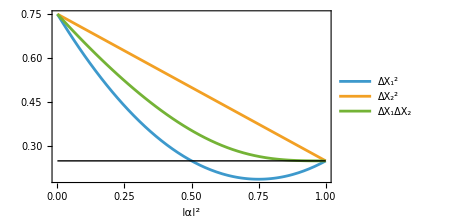

We can clearly see the first quadrature has squeezing for 1/2< |α|^2<1:

Reduce[(variances[[1]]/.ϕ->0)<1/4,x,Reals]

1/2<x<1

Minimum value:

FindMinimum[variances[[1]]/.ϕ->0,x]

{0.1875,{x→0.75}}

References

Use Chicago Style in your reference section. We have provided this References section for those who prefer in chapter reference sections.  However, generally we preferences to be at the end of the book as a Bibliography.  For citations within chapters, please use standard (Author, Date) in-text citation.